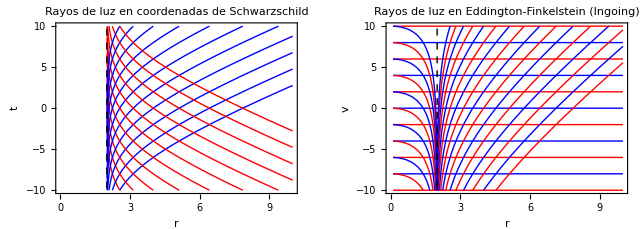

```mathematica
(*Definición de parámetros*)M=1; (*Masa del agujero negro*)
rs=2*M; (*Radio de Schwarzschild*)

(*Coordenada de tortuga r**)
rStar[r_]:=r+rs*Log[Abs[r/rs-1]];

(*Trayectorias de luz en Schwarzschild (t vs r)*)
(*t=constant\pm r**)
plotSchwarzschild=Plot[Evaluate[Table[{rStar[r]+c,-rStar[r]+c},{c,-10,10,2}]],{r,2.01,10},PlotRange->{{0,10},{-10,10}},PlotStyle->{Directive[Blue,Thin],Directive[Red,Thin]},Frame->True,FrameLabel->{"r","t"},PlotLabel->"Rayos de luz en coordenadas de Schwarzschild",Epilog->{Dashed,Black,InfiniteLine[{rs,0},{0,1}]}];

(*Trayectorias en Eddington-Finkelstein entrantes (v,r)*)
(*v=t+r* ,para rayos entrantes v=const,para salientes v=2r*+const*)
plotEF=Plot[Evaluate[Flatten[{Table[c,{c,-10,20,2}],(*Rayos entrantes*)Table[2*rStar[r]+c,{c,-20,10,2}] (*Rayos salientes*)}]],{r,0.1,10},PlotRange->{{0,10},{-10,10}},PlotStyle->{Directive[Red,Thin],Directive[Blue,Thin]},Frame->True,FrameLabel->{"r","v"},PlotLabel->"Rayos de luz en Eddington-Finkelstein (Ingoing)",Epilog->{Dashed,Black,InfiniteLine[{rs,0},{0,1}]}];

GraphicsRow[{plotSchwarzschild,plotEF}]
```